```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/okargaltsev/Dropbox/oyk100ivv101/CompPhys

Pallettes -> Other -> Basic Math Input

Write/Read data

```mathematica
Export["out.dat",{{5.7,4.3},{-1.2,7.8}},"CSV"]
```

out.dat

```mathematica
out=Import["out.dat","CSV"]
```

Vectors

```mathematica
vec1={1,3/4,4.5,4π}
```

{1,3/4,4.5,4 π}

```mathematica
vec1
```

{1,3/4,4.5,4 π}

```mathematica
N[vec1]
```

{1.,0.75,4.5,12.5664}

```mathematica
vec2=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
vec3=Range[0,20,2]
```

{0,2,4,6,8,10,12,14,16,18,20}

```mathematica
vec1+vec2
```

Thread::tdlen: Objects of unequal length in {1,3/4,4.5,4 π}+{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20} cannot be combined.

{1,3/4,4.5,4 π}+{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
vec4={2.,-5,0,14};
```

```mathematica
10vec1
```

{10,15/2,45.,40 π}

```mathematica
vec1-vec4
```

{-1.,23/4,4.5,-14+4 π}

```mathematica
vec1 vec4
```

{2.,-15/4,0.,56 π}

```mathematica
vec1.vec4
```

174.179

```mathematica
vec1[[1]]
```

1

```mathematica
vec1[[2;;4]]
```

{3/4,4.5,4 π}

```mathematica
awww=Select[vec1,#>2&]
```

{4.5,4 π}

```mathematica
#^2+3&[m]
```

3+m^2

```mathematica
#^2+3&@m
```

3+m^2

```mathematica
#>2&@1
```

False

```mathematica
#>2&/@{1,1.1,2,4,6}
```

{False,False,False,True,True}

```mathematica
Flatten[Position[vec1,#]&/@Select[vec1,#>2&]]
```

{3,4}

Arrays, Lists, Tables

```mathematica
Clear[out]
```

```mathematica
Dimensions[vec1]
```

{4}

```mathematica
tab=Table[n!,{n,1,20}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800,39916800,479001600,6227020800,87178291200,1307674368000,20922789888000,355687428096000,6402373705728000,121645100408832000,2432902008176640000}

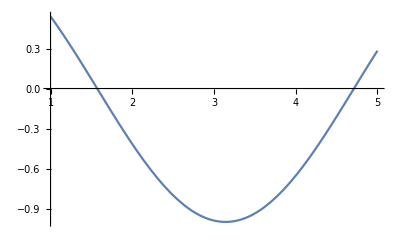

```mathematica
Plot[Cos[x],{x,1,5}]
```

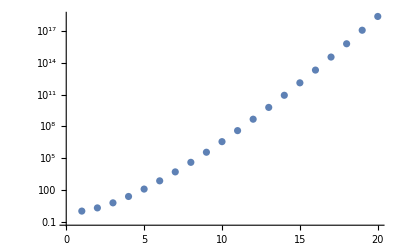

```mathematica
ListLogPlot[tab]
```

```mathematica
tab3d=Table[{i^2,j^2,k^2},{i,1,20},{j,1,20},{k,1,20}]
```

```mathematica
awwww=tab3d[[;;,3,;;]];
```

```mathematica
tab3d[[1,4,8]]
```

```mathematica
tab3d[[1,4;;12,-8]]
```

```mathematica
ImageData[-Graphics-][[1,1;;5]]
```

{{0.866667,0.545098,0.258824},{0.85098,0.529412,0.25098},{0.847059,0.533333,0.262745},{0.858824,0.545098,0.27451},{0.854902,0.541176,0.262745}}

### Plotting in 2 d and 3 d

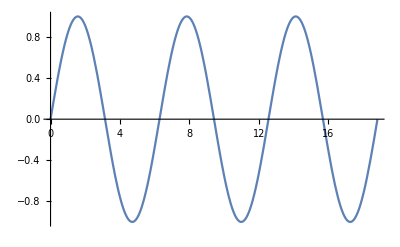

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

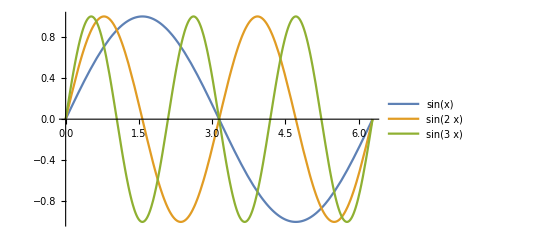

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

Complex signal plot

```mathematica
sig[t_]:=Piecewise[{{0.5Sin[2π 45 t],0.1<t<0.3},{Sin[2π 250 t],0.4<t<0.5},{Sin[2π 75 t],0.5<t<0.6},{Sin[2π 30 t]+Sin[2π 110t],0.7<t<0.9}}]+Piecewise[{{2 ⅇ^(-(t-0.2)^2/(2 0.001^2))-0.5Sin[2π 45 t],0.2-0.005<t<0.2+0.005}}]
```

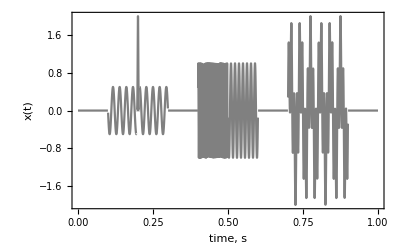

```mathematica
Plot[sig[t],{t,0,1},PlotRange->All,Frame->True,FrameLabel->{"time, s","x(t)"},PlotStyle->Gray,LabelStyle->{FontFamily->"Helvetica",12,GrayLevel[0.3]}]
```

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[ (x^2+y^2) Exp[1-x^2-y^2],{x, -3, 3},{y, -3, 3},PlotStyle->Opacity[0.5],Mesh->None,PlotPoints->50]
```

-Graphics3D-

```mathematica
c=ParametricPlot3D[{t,0,0},{t,-6 Pi,6 Pi},PlotRange->All,Boxed->False,Axes->False];
b=ParametricPlot3D[{t,0,0.1 t^2},{t,-6 Pi,6 Pi},PlotRange->All,Boxed->False,Axes->False];
a=ParametricPlot3D[{r Cos[θ],r Sin[θ],0.1 r^2},{θ,0,6 Pi},{r,0,17},PlotRange->All,Boxed->False,Axes->False,Mesh->None,PlotStyle->Opacity[0.1]];
Show[a,b,c]
```

-Graphics3D-

Dynamical manipulation

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2,0.5}]
```

```mathematica
Animate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]
```

```mathematica
Manipulate[Factor[2^n+1],{n,10,100,1}]
```

Histograms

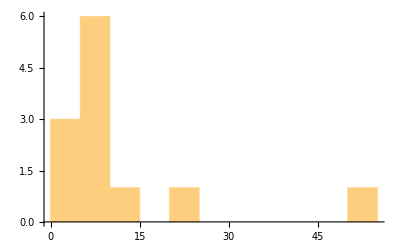

```mathematica
Histogram[{1,2,5,8,5,7,9,10,50,3,6,24}]
```

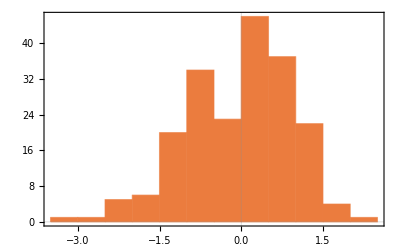

```mathematica
Histogram[RandomVariate[NormalDistribution[0,1],200],PlotTheme->"Scientific"]
```

```mathematica
data1=RandomVariate[NormalDistribution[0,1],500];
data2=RandomVariate[NormalDistribution[3,1/2],500];
```

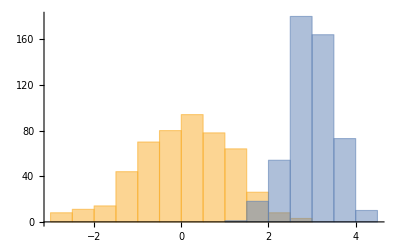

```mathematica
Histogram[{data1,data2}]
```

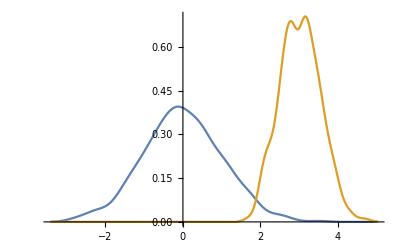

```mathematica
SmoothHistogram[{data1,data2}]
```

Random numbers

```mathematica
RandomReal[]
```

0.0833266

```mathematica
RandomReal[{-2,1},10]
```

{-0.763432,0.815729,-0.136444,-1.22545,0.184863,-0.677435,0.187846,-0.884541,-1.75895,-0.272787}

```mathematica
RandomInteger[{-10,20},{10,2}]
```

{{18,3},{2,-9},{-8,4},{6,13},{20,-3},{0,-3},{19,-3},{10,0},{4,-7},{7,12}}

```mathematica
ClearAll[a,b,c];
```

```mathematica
RandomChoice[{a,"Y",c},20]
```

{Y,Y,Y,Y,c,c,Y,a,Y,c,c,Y,c,Y,Y,a,Y,Y,a,c}

```mathematica
Range[30]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
RandomSample[Range[30],20]
```

{17,3,8,9,26,10,5,20,2,29,4,11,7,24,6,28,22,13,30,1}

RandomChoice - repetitions, RandomSample - no elements ever occur more than once

```mathematica
data=RandomVariate[NormalDistribution[1,3],10^4];
```

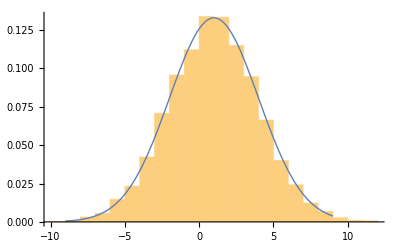

```mathematica
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[PDF[NormalDistribution[1,3],x],{x,-9,9},PlotStyle->Thick]]
```

```mathematica
Homogeneous Poisson process is a prosess in which the probability of event happening during the time interval dt remains the same for any interval.
```

```mathematica
Simulate a homogeneous (or inhomogeneous) Poisson processes (imagine a counting experiment with certain rate which changes as a function of time for inhomogeneous Poisson process). How to simulate the times when events are happening (e.g., a decay which produces photon which is registeres by the instrument)?
```

```mathematica
SeedRandom[34];
```

```mathematica
RandomFunction[PoissonProcess[1.3],{0,15},5]
```

TemporalData[…]

```mathematica
data=RandomFunction[PoissonProcess[1.3],{0,15},5]["TimeList"];
```

```mathematica
IPP[p_]:=InhomogeneousPoissonProcess[(1-p)/(2π)+p Sin[2π 2.3t],t]
```

```mathematica
data=RandomFunction[IPP[1],{0,100},300]["TimeList"];
```

```mathematica
Dimensions[data]
```

{300}

```mathematica
Length/@data
```

{5033,5030,5146,5005,4920,5050,5142,4988,4900,4938,5133,5004,5023,4862,4975,4943,5089,4870,5066,5018,4958,5143,5010,4962,4991,4959,4971,4918,4958,5039,5047,5019,5102,5121,4965,4894,4989,5055,5033,5012,5107,5021,4885,4909,4986,4965,4944,5029,4991,5054,5082,5064,5065,4972,5197,5002,4949,5018,4970,5067,5035,4927,4970,4962,4966,5103,4965,4919,4992,4920,4885,4895,5062,4904,4933,4965,5056,4901,5002,4902,5073,5057,5036,5073,4913,5124,5057,4976,5001,5117,4995,5136,5131,4924,5071,5006,4968,5023,5079,5011,4891,4944,5036,5072,5026,4957,4977,5189,4935,5075,5020,4942,5016,5015,4930,5011,4985,4935,5058,4963,4986,5078,4969,5034,4945,5008,5107,5102,5025,5097,4961,4965,4895,4969,4988,5136,5088,4878,4995,4986,4814,4963,5009,4975,5056,5034,5139,5013,5092,5109,5046,5009,4990,4971,5003,4979,5144,5197,4897,4996,4988,5039,5054,5050,5086,5018,5027,4865,4999,4922,5055,5072,5081,4966,5091,4898,5019,5055,4912,4939,5028,4899,5033,4926,5044,4991,5081,4993,4948,4957,4986,4979,5112,4861,4967,4937,5114,4957,4918,4943,5011,4962,5052,4978,4924,5001,5019,5094,4974,4901,5137,4937,4997,4971,5067,4977,5198,5009,5162,5029,4953,4972,4913,5039,4998,4940,5106,5059,5079,4989,4950,5105,5059,4987,5044,4920,5057,5026,5045,4880,5054,5038,4920,4987,4902,5075,5000,5124,4956,5009,5012,4930,5031,5006,5044,4941,4973,5032,5079,5021,4968,4971,4952,5124,4852,5102,4985,5065,5101,5051,4892,4898,5117,4967,5063,5042,5103,4990,4943,4972,5040,4848,4980,5059,5133,5009,5098,4995,4937,4922,4996,4923,4960,4922,4864,5007,4948,4963,4992,4980}

Be sure to  explore and understand the structure of the object called “TemporalData”   and read about it in Mathematica help. What kind of output does the command below produce?

What does this command do?

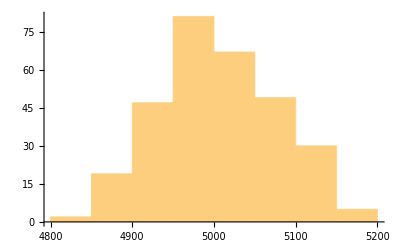

```mathematica
Histogram[Length/@data]
```

```mathematica
Generate randomly distributed points
```

```mathematica
ng=50;
```

```mathematica
g1={RandomVariate[NormalDistribution[-3.,.1],ng],RandomVariate[NormalDistribution[1.,1.],ng]}ᵀ;
g2={RandomVariate[NormalDistribution[3.,.1],ng],RandomVariate[NormalDistribution[1.,1.],ng]}ᵀ;
gtemp={RandomVariate[NormalDistribution[0,0.75],2ng],RandomVariate[NormalDistribution[0,0.75],2ng]}ᵀ;
g3=SortBy[gtemp,Total[#^2]&][[;;ng]];
g4=SortBy[gtemp,Total[#^2]&][[ng+1;;]];
g51=Subdivide[-2.75,2.75,ng];
g52=(g51/2)^2-4;
g5={g51,g52+RandomVariate[NormalDistribution[0,0.5],Length[g52]]}ᵀ;
data1={g1,g2,g3,g4,g5};
```

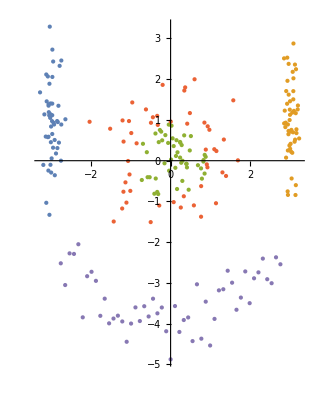

```mathematica
ListPlot[data1,PlotRange->All,AspectRatio->Automatic,PlotStyle->PointSize[Medium]]
```

What do the the commands below do?  Why is the Transpose operation needed?  Transpose[m] can be input as mᵀ.

```mathematica
Dimensions[data1]
```

{5}

```mathematica
data1
```

{{{-3.14093,1.45651},{-2.88875,2.57285},{-3.00693,1.60437},{-3.13897,1.08789},{-3.00283,1.70698},{-3.0419,0.378929},{-3.05477,-0.402612},{-3.10776,2.60726},{-2.9932,0.227154},{-2.90541,1.73412},{-3.04682,0.532068},{-3.2238,0.59498},{-3.05834,-1.36443},{-2.99229,-0.454588},{-2.97365,1.96017},{-3.06964,0.746764},{-2.93809,-0.413855},{-3.00281,1.60754},{-2.93982,1.01135},{-3.18163,0.31084},{-2.91507,0.974093},{-2.93427,0.333235},{-3.11232,1.00674},{-3.11099,0.630609},{-2.7297,1.24238},{-3.07405,0.0418865},{-2.90609,1.0422},{-3.04203,2.76439},{-3.09938,0.245333},{-2.96231,0.816741},{-3.00878,2.63012},{-2.96301,-0.996746},{-2.95275,-0.425745},{-3.02016,0.105107},{-3.08092,-0.643622},{-3.18606,0.444566},{-3.02835,1.85147},{-3.03915,1.4834},{-2.97455,1.21654},{-2.92871,2.0848},{-2.94605,1.47415},{-3.16257,-0.261818},{-3.04697,-0.026921},{-3.1248,0.0971509},{-2.90557,1.61428},{-3.04716,1.29692},{-3.09707,-0.816549},{-3.14272,-1.11761},{-2.82413,0.783899},{-3.04702,1.24042}},{{2.95973,1.23207},{2.91061,0.276429},{2.95213,0.844835},{2.963,1.66658},{2.94026,-0.354704},{2.89491,1.46676},{2.90563,0.626411},{3.09049,2.82436},{2.97228,0.827426},{2.71655,1.25858},{2.89707,1.17663},{3.1311,2.09639},{3.0819,-0.198481},{2.95662,-0.125377},{3.26555,0.176316},{2.90939,0.526284},{2.95724,1.15461},{2.95792,-0.835658},{2.8207,0.361114},{3.0276,-0.159449},{2.94234,2.51711},{3.21018,0.518956},{3.23968,0.227836},{3.04764,1.25411},{2.96886,0.255707},{2.9761,1.4685},{2.91069,2.02619},{2.95428,0.388431},{2.84861,-0.412189},{2.8154,-0.872617},{3.06031,0.331523},{2.8882,-0.345756},{2.89786,0.423855},{2.88787,0.138085},{2.95746,-0.447714},{3.18412,1.18802},{3.00142,0.920953},{2.89319,0.130537},{2.95792,2.02102},{2.9472,1.45382},{2.95158,0.48393},{3.11569,0.660709},{3.15086,1.69086},{2.9174,1.54446},{2.91858,1.08593},{3.04451,1.95216},{2.9085,1.91108},{2.93797,1.36896},{3.07495,1.04465},{2.90589,-0.659966}},{{0.020689,0.00898928},{-0.0596529,0.0134456},{0.0580119,0.0325469},{0.00513659,0.0704333},{0.0848557,0.100528},{0.072197,0.120443},{0.0415441,0.141807},{0.138494,-0.181068},{0.198161,-0.120873},{-0.184179,0.147081},{0.183046,0.210717},{0.189973,-0.280623},{0.272686,-0.219449},{-0.267158,-0.257692},{0.17965,-0.337941},{0.0190358,-0.394374},{-0.134763,-0.395812},{-0.259206,-0.334573},{-0.0625862,0.423394},{0.390551,-0.198739},{0.326059,0.32249},{-0.395391,0.246279},{0.127031,0.500715},{-0.420379,-0.312853},{0.000940167,0.54855},{-0.0237545,0.564972},{-0.368116,-0.442574},{-0.489207,-0.362782},{-0.600415,-0.103416},{0.496627,-0.35622},{-0.199069,-0.588153},{-0.580763,-0.252476},{0.274798,-0.629077},{0.397117,-0.574439},{-0.420372,0.560857},{0.175298,0.688422},{-0.699746,-0.155796},{-0.491025,-0.525236},{0.607397,-0.385581},{0.42325,-0.605695},{-0.700564,0.254937},{0.591962,-0.453288},{0.7246,0.176524},{0.699305,0.271905},{0.355841,0.679795},{-0.76148,0.283519},{0.341001,0.763082},{0.495622,0.696499},{0.166055,-0.867429},{-0.584071,0.667466}},{{-0.774731,-0.445856},{0.421251,0.789577},{-0.877758,0.196419},{0.671447,0.600213},{-0.910293,0.191054},{-0.65733,0.664103},{-0.00948864,-0.938939},{0.935068,-0.14219},{0.806098,0.505948},{-0.0425955,-0.951426},{0.734142,-0.618568},{-0.625345,-0.781961},{-1.01471,-0.148699},{0.230423,1.00336},{1.0401,0.38479},{1.1209,0.0395747},{0.359686,1.09025},{1.0064,0.556664},{-0.059202,-1.16015},{-0.605191,-1.02863},{-0.689991,-1.01852},{0.212164,-1.21902},{0.275899,-1.20879},{1.25024,-0.010476},{0.65842,-1.06482},{-1.27043,0.159961},{1.24883,-0.321285},{-1.02419,0.792565},{-0.309226,1.27977},{1.21628,-0.527528},{0.0271833,-1.34968},{0.831239,-1.07742},{-1.13795,0.758157},{-0.827448,-1.11573},{-0.885758,1.12469},{1.37684,-0.401308},{0.745517,-1.22778},{-1.28455,0.715474},{0.206051,1.51534},{-0.233303,1.54457},{-0.498981,1.4897},{-1.49435,-0.485941},{1.45099,-0.618039},{1.55987,0.315803},{0.314943,1.60615},{-0.446702,1.62251},{-0.839548,-1.68682},{1.84628,-0.659325},{1.8247,-1.39883},{1.34196,-2.53948}},{{-2.75,-2.04557},{-2.64,-2.3661},{-2.53,-1.5972},{-2.42,-2.53416},{-2.31,-2.76967},{-2.2,-2.36527},{-2.09,-2.61398},{-1.98,-2.98365},{-1.87,-2.76774},{-1.76,-3.48692},{-1.65,-3.39773},{-1.54,-3.88622},{-1.43,-3.39358},{-1.32,-2.847},{-1.21,-3.55689},{-1.1,-3.91372},{-0.99,-4.20714},{-0.88,-3.66432},{-0.77,-3.14069},{-0.66,-3.97315},{-0.55,-4.05762},{-0.44,-3.61631},{-0.33,-4.52838},{-0.22,-3.90327},{-0.11,-3.72459},{0.,-3.16325},{0.11,-4.07346},{0.22,-4.5296},{0.33,-4.33783},{0.44,-4.05892},{0.55,-4.68488},{0.66,-3.56358},{0.77,-4.09089},{0.88,-3.48685},{0.99,-3.44375},{1.1,-3.64656},{1.21,-2.87078},{1.32,-3.99611},{1.43,-3.50592},{1.54,-3.09915},{1.65,-2.83406},{1.76,-2.63885},{1.87,-3.64307},{1.98,-3.23314},{2.09,-2.11152},{2.2,-3.15501},{2.31,-2.51249},{2.42,-2.91741},{2.53,-3.19077},{2.64,-0.737721},{2.75,-2.92272}}}

```mathematica
data=Flatten[data1,1];
```

```mathematica
Dimensions[data]
```

{251,2}

```mathematica
data
```

{{-3.14093,1.45651},{-2.88875,2.57285},{-3.00693,1.60437},{-3.13897,1.08789},{-3.00283,1.70698},{-3.0419,0.378929},{-3.05477,-0.402612},{-3.10776,2.60726},{-2.9932,0.227154},{-2.90541,1.73412},{-3.04682,0.532068},{-3.2238,0.59498},{-3.05834,-1.36443},{-2.99229,-0.454588},{-2.97365,1.96017},{-3.06964,0.746764},{-2.93809,-0.413855},{-3.00281,1.60754},{-2.93982,1.01135},{-3.18163,0.31084},{-2.91507,0.974093},{-2.93427,0.333235},{-3.11232,1.00674},{-3.11099,0.630609},{-2.7297,1.24238},{-3.07405,0.0418865},{-2.90609,1.0422},{-3.04203,2.76439},{-3.09938,0.245333},{-2.96231,0.816741},{-3.00878,2.63012},{-2.96301,-0.996746},{-2.95275,-0.425745},{-3.02016,0.105107},{-3.08092,-0.643622},{-3.18606,0.444566},{-3.02835,1.85147},{-3.03915,1.4834},{-2.97455,1.21654},{-2.92871,2.0848},{-2.94605,1.47415},{-3.16257,-0.261818},{-3.04697,-0.026921},{-3.1248,0.0971509},{-2.90557,1.61428},{-3.04716,1.29692},{-3.09707,-0.816549},{-3.14272,-1.11761},{-2.82413,0.783899},{-3.04702,1.24042},{2.95973,1.23207},{2.91061,0.276429},{2.95213,0.844835},{2.963,1.66658},{2.94026,-0.354704},{2.89491,1.46676},{2.90563,0.626411},{3.09049,2.82436},{2.97228,0.827426},{2.71655,1.25858},{2.89707,1.17663},{3.1311,2.09639},{3.0819,-0.198481},{2.95662,-0.125377},{3.26555,0.176316},{2.90939,0.526284},{2.95724,1.15461},{2.95792,-0.835658},{2.8207,0.361114},{3.0276,-0.159449},{2.94234,2.51711},{3.21018,0.518956},{3.23968,0.227836},{3.04764,1.25411},{2.96886,0.255707},{2.9761,1.4685},{2.91069,2.02619},{2.95428,0.388431},{2.84861,-0.412189},{2.8154,-0.872617},{3.06031,0.331523},{2.8882,-0.345756},{2.89786,0.423855},{2.88787,0.138085},{2.95746,-0.447714},{3.18412,1.18802},{3.00142,0.920953},{2.89319,0.130537},{2.95792,2.02102},{2.9472,1.45382},{2.95158,0.48393},{3.11569,0.660709},{3.15086,1.69086},{2.9174,1.54446},{2.91858,1.08593},{3.04451,1.95216},{2.9085,1.91108},{2.93797,1.36896},{3.07495,1.04465},{2.90589,-0.659966},{0.020689,0.00898928},{-0.0596529,0.0134456},{0.0580119,0.0325469},{0.00513659,0.0704333},{0.0848557,0.100528},{0.072197,0.120443},{0.0415441,0.141807},{0.138494,-0.181068},{0.198161,-0.120873},{-0.184179,0.147081},{0.183046,0.210717},{0.189973,-0.280623},{0.272686,-0.219449},{-0.267158,-0.257692},{0.17965,-0.337941},{0.0190358,-0.394374},{-0.134763,-0.395812},{-0.259206,-0.334573},{-0.0625862,0.423394},{0.390551,-0.198739},{0.326059,0.32249},{-0.395391,0.246279},{0.127031,0.500715},{-0.420379,-0.312853},{0.000940167,0.54855},{-0.0237545,0.564972},{-0.368116,-0.442574},{-0.489207,-0.362782},{-0.600415,-0.103416},{0.496627,-0.35622},{-0.199069,-0.588153},{-0.580763,-0.252476},{0.274798,-0.629077},{0.397117,-0.574439},{-0.420372,0.560857},{0.175298,0.688422},{-0.699746,-0.155796},{-0.491025,-0.525236},{0.607397,-0.385581},{0.42325,-0.605695},{-0.700564,0.254937},{0.591962,-0.453288},{0.7246,0.176524},{0.699305,0.271905},{0.355841,0.679795},{-0.76148,0.283519},{0.341001,0.763082},{0.495622,0.696499},{0.166055,-0.867429},{-0.584071,0.667466},{-0.774731,-0.445856},{0.421251,0.789577},{-0.877758,0.196419},{0.671447,0.600213},{-0.910293,0.191054},{-0.65733,0.664103},{-0.00948864,-0.938939},{0.935068,-0.14219},{0.806098,0.505948},{-0.0425955,-0.951426},{0.734142,-0.618568},{-0.625345,-0.781961},{-1.01471,-0.148699},{0.230423,1.00336},{1.0401,0.38479},{1.1209,0.0395747},{0.359686,1.09025},{1.0064,0.556664},{-0.059202,-1.16015},{-0.605191,-1.02863},{-0.689991,-1.01852},{0.212164,-1.21902},{0.275899,-1.20879},{1.25024,-0.010476},{0.65842,-1.06482},{-1.27043,0.159961},{1.24883,-0.321285},{-1.02419,0.792565},{-0.309226,1.27977},{1.21628,-0.527528},{0.0271833,-1.34968},{0.831239,-1.07742},{-1.13795,0.758157},{-0.827448,-1.11573},{-0.885758,1.12469},{1.37684,-0.401308},{0.745517,-1.22778},{-1.28455,0.715474},{0.206051,1.51534},{-0.233303,1.54457},{-0.498981,1.4897},{-1.49435,-0.485941},{1.45099,-0.618039},{1.55987,0.315803},{0.314943,1.60615},{-0.446702,1.62251},{-0.839548,-1.68682},{1.84628,-0.659325},{1.8247,-1.39883},{1.34196,-2.53948},{-2.75,-2.04557},{-2.64,-2.3661},{-2.53,-1.5972},{-2.42,-2.53416},{-2.31,-2.76967},{-2.2,-2.36527},{-2.09,-2.61398},{-1.98,-2.98365},{-1.87,-2.76774},{-1.76,-3.48692},{-1.65,-3.39773},{-1.54,-3.88622},{-1.43,-3.39358},{-1.32,-2.847},{-1.21,-3.55689},{-1.1,-3.91372},{-0.99,-4.20714},{-0.88,-3.66432},{-0.77,-3.14069},{-0.66,-3.97315},{-0.55,-4.05762},{-0.44,-3.61631},{-0.33,-4.52838},{-0.22,-3.90327},{-0.11,-3.72459},{0.,-3.16325},{0.11,-4.07346},{0.22,-4.5296},{0.33,-4.33783},{0.44,-4.05892},{0.55,-4.68488},{0.66,-3.56358},{0.77,-4.09089},{0.88,-3.48685},{0.99,-3.44375},{1.1,-3.64656},{1.21,-2.87078},{1.32,-3.99611},{1.43,-3.50592},{1.54,-3.09915},{1.65,-2.83406},{1.76,-2.63885},{1.87,-3.64307},{1.98,-3.23314},{2.09,-2.11152},{2.2,-3.15501},{2.31,-2.51249},{2.42,-2.91741},{2.53,-3.19077},{2.64,-0.737721},{2.75,-2.92272}}

```mathematica
Dimensions[dataᵀ]
```

{2,251}

```mathematica
dataᵀ
```

{{-3.14093,-2.88875,-3.00693,-3.13897,-3.00283,-3.0419,-3.05477,-3.10776,-2.9932,-2.90541,-3.04682,-3.2238,-3.05834,-2.99229,-2.97365,-3.06964,-2.93809,-3.00281,-2.93982,-3.18163,-2.91507,-2.93427,-3.11232,-3.11099,-2.7297,-3.07405,-2.90609,-3.04203,-3.09938,-2.96231,-3.00878,-2.96301,-2.95275,-3.02016,-3.08092,-3.18606,-3.02835,-3.03915,-2.97455,-2.92871,-2.94605,-3.16257,-3.04697,-3.1248,-2.90557,-3.04716,-3.09707,-3.14272,-2.82413,-3.04702,2.95973,2.91061,2.95213,2.963,2.94026,2.89491,2.90563,3.09049,2.97228,2.71655,2.89707,3.1311,3.0819,2.95662,3.26555,2.90939,2.95724,2.95792,2.8207,3.0276,2.94234,3.21018,3.23968,3.04764,2.96886,2.9761,2.91069,2.95428,2.84861,2.8154,3.06031,2.8882,2.89786,2.88787,2.95746,3.18412,3.00142,2.89319,2.95792,2.9472,2.95158,3.11569,3.15086,2.9174,2.91858,3.04451,2.9085,2.93797,3.07495,2.90589,0.020689,-0.0596529,0.0580119,0.00513659,0.0848557,0.072197,0.0415441,0.138494,0.198161,-0.184179,0.183046,0.189973,0.272686,-0.267158,0.17965,0.0190358,-0.134763,-0.259206,-0.0625862,0.390551,0.326059,-0.395391,0.127031,-0.420379,0.000940167,-0.0237545,-0.368116,-0.489207,-0.600415,0.496627,-0.199069,-0.580763,0.274798,0.397117,-0.420372,0.175298,-0.699746,-0.491025,0.607397,0.42325,-0.700564,0.591962,0.7246,0.699305,0.355841,-0.76148,0.341001,0.495622,0.166055,-0.584071,-0.774731,0.421251,-0.877758,0.671447,-0.910293,-0.65733,-0.00948864,0.935068,0.806098,-0.0425955,0.734142,-0.625345,-1.01471,0.230423,1.0401,1.1209,0.359686,1.0064,-0.059202,-0.605191,-0.689991,0.212164,0.275899,1.25024,0.65842,-1.27043,1.24883,-1.02419,-0.309226,1.21628,0.0271833,0.831239,-1.13795,-0.827448,-0.885758,1.37684,0.745517,-1.28455,0.206051,-0.233303,-0.498981,-1.49435,1.45099,1.55987,0.314943,-0.446702,-0.839548,1.84628,1.8247,1.34196,-2.75,-2.64,-2.53,-2.42,-2.31,-2.2,-2.09,-1.98,-1.87,-1.76,-1.65,-1.54,-1.43,-1.32,-1.21,-1.1,-0.99,-0.88,-0.77,-0.66,-0.55,-0.44,-0.33,-0.22,-0.11,0.,0.11,0.22,0.33,0.44,0.55,0.66,0.77,0.88,0.99,1.1,1.21,1.32,1.43,1.54,1.65,1.76,1.87,1.98,2.09,2.2,2.31,2.42,2.53,2.64,2.75},{1.45651,2.57285,1.60437,1.08789,1.70698,0.378929,-0.402612,2.60726,0.227154,1.73412,0.532068,0.59498,-1.36443,-0.454588,1.96017,0.746764,-0.413855,1.60754,1.01135,0.31084,0.974093,0.333235,1.00674,0.630609,1.24238,0.0418865,1.0422,2.76439,0.245333,0.816741,2.63012,-0.996746,-0.425745,0.105107,-0.643622,0.444566,1.85147,1.4834,1.21654,2.0848,1.47415,-0.261818,-0.026921,0.0971509,1.61428,1.29692,-0.816549,-1.11761,0.783899,1.24042,1.23207,0.276429,0.844835,1.66658,-0.354704,1.46676,0.626411,2.82436,0.827426,1.25858,1.17663,2.09639,-0.198481,-0.125377,0.176316,0.526284,1.15461,-0.835658,0.361114,-0.159449,2.51711,0.518956,0.227836,1.25411,0.255707,1.4685,2.02619,0.388431,-0.412189,-0.872617,0.331523,-0.345756,0.423855,0.138085,-0.447714,1.18802,0.920953,0.130537,2.02102,1.45382,0.48393,0.660709,1.69086,1.54446,1.08593,1.95216,1.91108,1.36896,1.04465,-0.659966,0.00898928,0.0134456,0.0325469,0.0704333,0.100528,0.120443,0.141807,-0.181068,-0.120873,0.147081,0.210717,-0.280623,-0.219449,-0.257692,-0.337941,-0.394374,-0.395812,-0.334573,0.423394,-0.198739,0.32249,0.246279,0.500715,-0.312853,0.54855,0.564972,-0.442574,-0.362782,-0.103416,-0.35622,-0.588153,-0.252476,-0.629077,-0.574439,0.560857,0.688422,-0.155796,-0.525236,-0.385581,-0.605695,0.254937,-0.453288,0.176524,0.271905,0.679795,0.283519,0.763082,0.696499,-0.867429,0.667466,-0.445856,0.789577,0.196419,0.600213,0.191054,0.664103,-0.938939,-0.14219,0.505948,-0.951426,-0.618568,-0.781961,-0.148699,1.00336,0.38479,0.0395747,1.09025,0.556664,-1.16015,-1.02863,-1.01852,-1.21902,-1.20879,-0.010476,-1.06482,0.159961,-0.321285,0.792565,1.27977,-0.527528,-1.34968,-1.07742,0.758157,-1.11573,1.12469,-0.401308,-1.22778,0.715474,1.51534,1.54457,1.4897,-0.485941,-0.618039,0.315803,1.60615,1.62251,-1.68682,-0.659325,-1.39883,-2.53948,-2.04557,-2.3661,-1.5972,-2.53416,-2.76967,-2.36527,-2.61398,-2.98365,-2.76774,-3.48692,-3.39773,-3.88622,-3.39358,-2.847,-3.55689,-3.91372,-4.20714,-3.66432,-3.14069,-3.97315,-4.05762,-3.61631,-4.52838,-3.90327,-3.72459,-3.16325,-4.07346,-4.5296,-4.33783,-4.05892,-4.68488,-3.56358,-4.09089,-3.48685,-3.44375,-3.64656,-2.87078,-3.99611,-3.50592,-3.09915,-2.83406,-2.63885,-3.64307,-3.23314,-2.11152,-3.15501,-2.51249,-2.91741,-3.19077,-0.737721,-2.92272}}

```mathematica
MinMax[dataᵀ]
```

{-4.68488,3.26555}

```mathematica
mm=MinMax/@(dataᵀ)
```

{{-3.2238,3.26555},{-4.68488,2.82436}}

Functions

```mathematica
f[x_]:=x^2+3Sin[x^2];
```

```mathematica
f[5.]
```

24.6029

```mathematica
N[f[5]]
```

24.6029

```mathematica
f[5.]
```

24.6029

```mathematica
#^2+3Sin[#^2]&
```

#1^2+3 Sin[#1^2]&

```mathematica
Map[f,{a,b,c,d,e}]
```

```mathematica
f/@{a,b,c,d,e}
```

```mathematica
N[#^2+3Sin[#^2]&/@{5.,7,6.}]
```

Equations

```mathematica
Solve[a x^2+b x+c==0,x]
```

```mathematica
Clear[x,y]
```

```mathematica
Solve[f[x]==x,x]
```

```mathematica
NSolve[f[t]==t,t,Reals]
```

```mathematica
Solve[a x+y==7&&b x-y==1,{x,y}]
```

{{x→8/(a+b),y→-(a-7 b)/(a+b)}}

```mathematica
sol=NSolve[{x^2+y^3==1,2x+3y==4},{x,y}]
```

{{x→7.93641,y→-3.95761},{x→0.719295-0.255679 ⅈ,y→0.853803+0.170453 ⅈ},{x→0.719295+0.255679 ⅈ,y→0.853803-0.170453 ⅈ}}

```mathematica
sol[[2,1,2]]
```

0.719295-0.255679 ⅈ

### ReplaceAll ( /. )

```mathematica
x+y/.sol[[2]]
```

1.5731-0.0852263 ⅈ

### Systems of linear equations

```mathematica
A=Table[RandomReal[{0,i}]+j^2,{i,4},{j,4}];
```

```mathematica
MatrixForm[A]
```

(1.08094 | 4.80912 | 9.62553 | 16.0614
2.81121 | 4.49869 | 10.7597 | 17.8544
1.83224 | 6.03781 | 10.1291 | 17.9576
4.62246 | 7.86563 | 11.1146 | 16.5844)

```mathematica
b=Table[1,4]
```

{1,1,1,1}

```mathematica
Inverse[A]
```

{{-0.707612,0.391299,0.175108,0.0744239},{0.0463492,-0.442228,0.252175,0.158152},{1.11778,-0.0762118,-1.14425,0.238517},{-0.573878,0.151751,0.598456,-0.195305}}

```mathematica
Inverse[A].b
```

{-0.0667811,0.014448,0.135834,-0.0189756}

### Differential equations

```mathematica
DSolve[{x''[t]==a,x'[0]==v0,x[0]==x0},x[t],t]
```

{{x[t]→1/2 (a t^2+2 t v0+2 x0)}}

```mathematica
DSolve[y'[x]+y[x]==a Sin[x],y[x],x]
```

{{y[x]→ⅇ^-x C[1]+1/2 a (-Cos[x]+Sin[x])}}

```mathematica
Clear[t]
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{x[t],y[t]}/.NDSolve[{y'[t]==-4x[t]-Cos[2t],x'[t]==y[t],x[0]==p0[[1]],y[0]==p0[[2]]},{x,y},{t,20}]],{t,0,20},PlotRange->All],{{p0,{1,1}},Locator},SaveDefinitions->True]
```

Integration

```mathematica
Clear[n]
```

```mathematica
Integrate[x^n,x]
```

```mathematica
Integrate[Exp[-x^2.],{x,0,Infinity}]
```

```mathematica
∫_0^∞ ⅇ^(-x^2)ⅆx
```

```mathematica
Integrate[Exp[-x^2-y^2],{x,-Infinity,Infinity}, {y,-Infinity,Infinity}]
```

```mathematica
∫ⅇ^(-x Sin[x]^2)ⅆx
```

```mathematica
N[∫_0^∞ ⅇ^(-x Sin[x]^2)ⅆx]
```

Interpolation

```mathematica
tab=Table[Sin[x],{x,0,2π,0.1}]
```

{0.,0.0998334,0.198669,0.29552,0.389418,0.479426,0.564642,0.644218,0.717356,0.783327,0.841471,0.891207,0.932039,0.963558,0.98545,0.997495,0.999574,0.991665,0.973848,0.9463,0.909297,0.863209,0.808496,0.745705,0.675463,0.598472,0.515501,0.42738,0.334988,0.239249,0.14112,0.0415807,-0.0583741,-0.157746,-0.255541,-0.350783,-0.44252,-0.529836,-0.611858,-0.687766,-0.756802,-0.818277,-0.871576,-0.916166,-0.951602,-0.97753,-0.993691,-0.999923,-0.996165,-0.982453,-0.958924,-0.925815,-0.883455,-0.832267,-0.772764,-0.70554,-0.631267,-0.550686,-0.464602,-0.373877,-0.279415,-0.182163,-0.0830894}

```mathematica
f=Interpolation[tab]
```

InterpolatingFunction[{{1., 63.}}, <>]

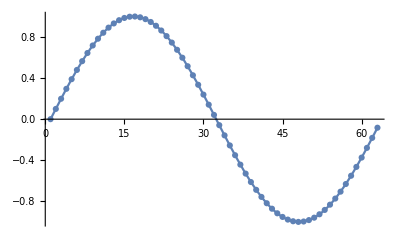

```mathematica
Show[Plot[f[x],{x,1,63}],ListPlot[tab]]
```

```mathematica
tab=Table[{x,Sin[x^2]},{x,0,4π,0.1}];
```

```mathematica
f=Interpolation[tab]
```

InterpolatingFunction[{{0., 12.5}}, <>]

```mathematica
f[0.3333]
```

0.110875

```mathematica
Sin[0.3333^2]
```

0.110861

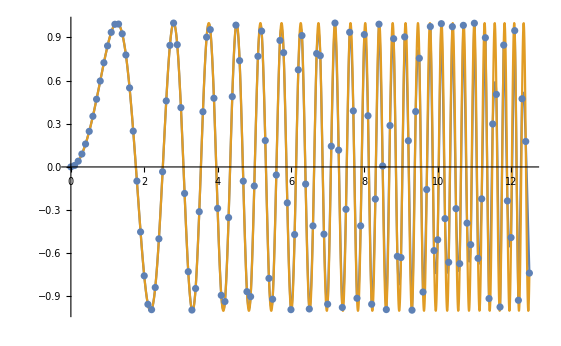

```mathematica
Show[Plot[{f[x],Sin[x^2]},{x,0,12.5}],ListPlot[tab]]
```

Fitting

```mathematica
data={{0,1},{1,0},{3,2},{5,4}};
```

```mathematica
line = Fit[data, {1,x,x^7},x]
```

0.440614+0.406728 x+0.0000196355 x^7

```mathematica
data=Table[{x,Sin[2π x]+Sin[3π x^2]+0.2RandomReal[]},{x,0,4,0.1}];
```

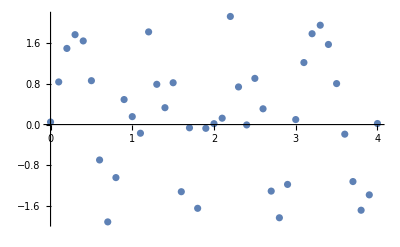

```mathematica
ListPlot[data]
```

```mathematica
errors=RandomReal[{0,0.2},Length[data]]
```

{0.154614,0.0709821,0.0182007,0.068085,0.04434,0.078707,0.00145636,0.0968583,0.155378,0.0118889,0.103413,0.0990452,0.0618461,0.0747232,0.123292,0.0413149,0.0573641,0.02659,0.0251632,0.0969314,0.131186,0.181021,0.151304,0.0939864,0.0323265,0.0226134,0.0921461,0.163706,0.0570885,0.0887074,0.0425885,0.0541657,0.168848,0.0428832,0.0468486,0.171938,0.153364,0.0870186,0.0675698,0.184576,0.133339}

```mathematica
Needs["ErrorBarPlots`"]
```

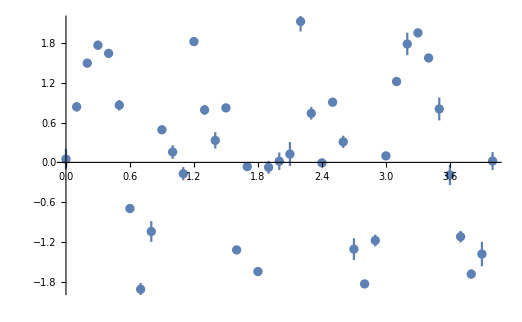

```mathematica
f1=ErrorListPlot[{data,ErrorBar/@errors}ᵀ]
```

```mathematica
Clear[b]
```

```mathematica
nlm=NonlinearModelFit[data,a Sin[2π ω x]+b Sin[3π x^2],{a,b,ω},x,Weights->1/errors^2]
```

FittedModel[0.829222 Sin[6.19308 x]+1.00867 Sin[3 π x^2]]

```mathematica
nlm[{"BestFit","ParameterTable"}]
```

{0.829222 Sin[6.19308 x]+1.00867 Sin[3 π x^2], | Estimate | Standard Error | t-Statistic | P-Value
a | 0.829222 | 0.0217595 | 38.1085 | 6.89376×10^-32
b | 1.00867 | 0.0348917 | 28.9086 | 1.77133×10^-27
ω | 0.985659 | 0.00383086 | 257.294 | 3.3428×10^-63}

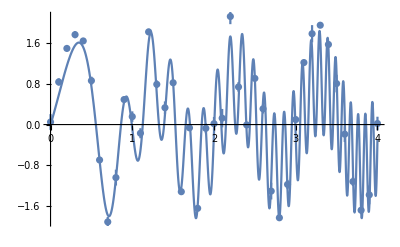

```mathematica
Show[f1,Plot[nlm[x],{x,0,4}]]
```

```mathematica
nlm["ParameterConfidenceIntervals"]
```

{{0.785172,0.873272},{0.938035,1.0793},{0.977904,0.993414}}

```mathematica
nlm["ANOVATable"]
```

| DF | SS | MS
Model | 3 | 252062. | 84020.5
Error | 38 | 740.069 | 19.4755
Uncorrected Total | 41 | 252802. | 
Corrected Total | 40 | 48867.6 |

Conditionals

```mathematica
If[7>8,x,y]
```

y

```mathematica
{6,-7,3,2,-1,-2}/.x_/;x<0->w
```

{6,w,3,2,w,w}

Loops

```mathematica
For[i=0,i<4,i++,Print[i]]
```

0

1

2

3

```mathematica
t=x;Do[t=1/(1+t),{10}];t
```

1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x))))))))))

Procedures

Module[] allows one to have a local variable (by all default variables in Mathematica are global)

```mathematica
f[v_]:=1+(v)^2;
```

```mathematica
f[v_]:=Module[{t},t=(1+v)^2;t=Expand[t]]
```

```mathematica
ff[v_]:=Module[{t},t=(1+v)^2;t=Expand[t]]
```

```mathematica
ff[(x+1)^2]
```

4+8 x+8 x^2+4 x^3+x^4

Greatest common divider for 2 numbers (Euler’s method)

```mathematica
gcd[m0_,n0_]:=
Module[{m=m0,n=n0},
While[n≠0,{m,n}={n,Mod[m,n]}];
m
]
```